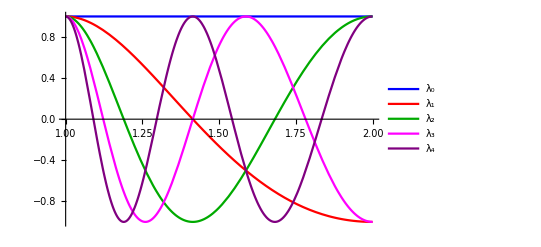

```mathematica
Plot[{Cos[0],Cos[(Pi Log[x])/Log[2]], Cos[(2 Pi Log[x])/Log[2]], Cos[(3 Pi Log[x])/Log[2]], Cos[(4 Pi Log[x])/Log[2]]},{x, 1,2}, PlotStyle->{Blue, Red , Darker[Green], Magenta, Purple}, PlotLegends->{Subscript[λ,"0"],Subscript[λ,"1"],Subscript[λ,"2"],Subscript[λ,"3"],Subscript[λ,"4"]}]
```

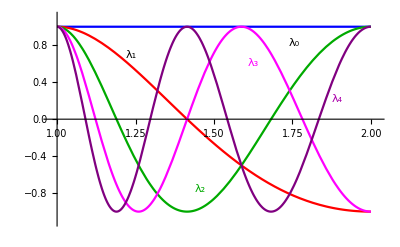

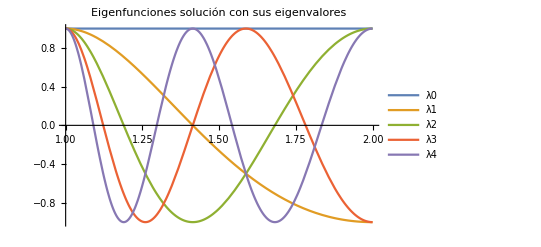

```mathematica
f[n_,x_]:=Cos[(n Pi Log[x])/Log[2]];
labels=Row[{λ, #}]&/@Range[0,4];
Plot[Evaluate@Table[f[n,x],{n,0,4}],{x,1,2},  PlotLabel->Style["Eigenfunciones solución con sus eigenvalores",FontSize->14],PlotLegends->labels]
```